0.9

1.1

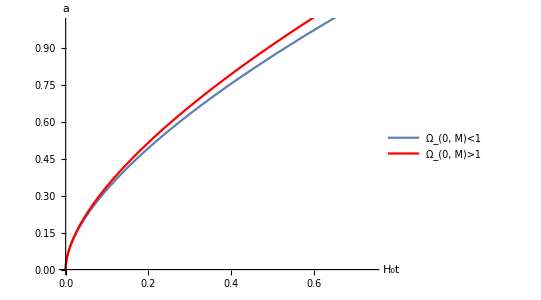

Radiation_matter_universe.pdf

```mathematica
Subscript[Ω, 1]=0.9
Subscript[Ω, 2]=1.1
p2 =Show[ParametricPlot[{{(2(1-Subscript[Ω, 1])^(3/2))/(3 Subscript[Ω, 1]^2)*((t-2)*Sqrt[1+t]+2),(1-Subscript[Ω, 1])/Subscript[Ω, 1] t}},{t,0,10},PlotLegends->{"Ω_(0, M)<1"}],ParametricPlot[{{(2(Subscript[Ω, 2]-1)^(3/2))/(3 Subscript[Ω, 2]^2)*((t-2)*Sqrt[1+t]+2),(Subscript[Ω, 2]-1)/Subscript[Ω, 2] t}},{t,0,12},PlotStyle->Red,PlotLegends->{"Ω_(0, M)>1"}],PlotRange->{0,1},AspectRatio->0.75,AxesLabel->{"H_0t",a}]
Export["Radiation_matter_universe.pdf",p2]
```